钱昌本 例103 check

```mathematica
DSolve[{y'[x]==z[x],z'[x]==-y[x],y[0]==0,z[0]==1},{y[x],z[x]},x]
```

{{y[x]→Sin[x],z[x]→Cos[x]}}

```mathematica
DSolve[{f'[x]==f[x]/x+4,f[1]==0},f[x],x]
```

{{f[x]→4 x Log[x]}}

钱昌本 例105 check

```mathematica
f[x_]=-1+x Log[1+1/x]+Log[(1+2 x)/(2 x)]
D[f[x],x]//FullSimplify
D[f[x],{x,2}]//FullSimplify
```

-1+x Log[1+1/x]+Log[(1+2 x)/(2 x)]

-1/x+1/(1+3 x+2 x^2)+Log[1+1/x]

(1+5 x (1+x))/(x^2 (1+x)^2 (1+2 x)^2)

```mathematica
g[x_]=-1+x Log[1+1/x]+Log[(2+2 x)/(2 x + 1)]
D[g[x],x]//FullSimplify
D[g[x],{x,2}]//FullSimplify
```

-1+x Log[1+1/x]+Log[(2+2 x)/(1+2 x)]

-2/(1+2 x)+Log[1+1/x]

-1/(x (1+x) (1+2 x)^2)

```mathematica
Series[Log[x+1],{x,0,5}]
Series[Log[-x+1],{x,0,5}]
Series[Log[(x+1)/(-x+1)],{x,0,5}]
```

x-x^2/2+x^3/3-x^4/4+x^5/5+O[x]^6

-x-x^2/2-x^3/3-x^4/4-x^5/5+O[x]^6

2 x+(2 x^3)/3+(2 x^5)/5+O[x]^6

{{1,2},{2,9/4},{3,64/27},{4,625/256},{5,7776/3125},{6,117649/46656},{7,2097152/823543},{8,43046721/16777216},{9,1000000000/387420489},{10,25937424601/10000000000}}

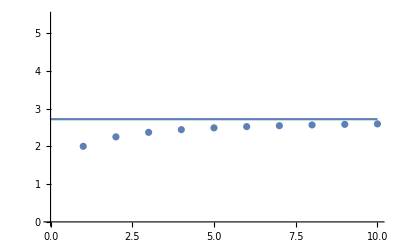

```mathematica
y[n_]:=(1+1/n)^n;
lim=10;
s1= Table[{n,y[n]},{n,1,lim}]
Show[Plot[E,{x,0,lim}],ListPlot[s1]]
```

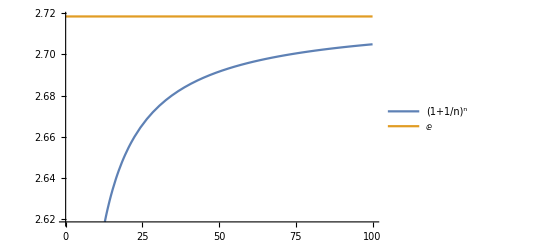

```mathematica
Plot[{(1+1/n)^n,Evaluate[Limit[(1+1/n)^n,n->Infinity]]},{n,0,100},PlotLegends->"Expressions"]
```